LUCAS LARSSON, DENNIS HADZIALIC
INLÄMNINGSUPPGIFT 1 

Polyniomekvationen:

```mathematica
polynom= 
Solve[x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20==0,x]
```

{{x→-5},{x→-3},{x→-2},{x→1/3},{x→2}}

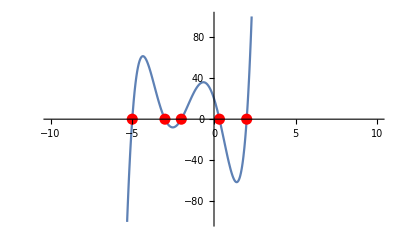

```mathematica
p1 = Plot[
x^5+(23/3)*x^4+(25/3)*x^3-(107/3)*x^2-(148/3)*x+20==0,
{x,-10,10}, PlotRange->{-100,100}, Epilog->{
Red, PointSize[0.02],
Point[{{-5,0},{-3,0},{-2,0},{1/3,0},{2,0}}]
}
]
```

### Olikhet:

### Uppgift 9

```mathematica
A)
```

```mathematica
Reduce[2+x>6 x^2]
```

-1/2<x<2/3

B)

```mathematica
Reduce[(1+x)/((-2+x) (3+2 x))≥0]
```

-3/2<x≤-1||x>2

C)

```mathematica
Reduce[(x^2-5)/(x-1)≤-1]
```

x≤-3||1<x≤2

D)

```mathematica
Reduce[-√(x^2+9)≥2 √x+4]
```

False

E)

```mathematica
Reduce[√(3x+3)≥√x+1]
```

x≥0

```mathematica
Uppgift 10
```

A)

```mathematica
Reduce[x^3<1&&-6-x+x^2≥0]
```

x≤-2

B)

```mathematica
Reduce[(2x-1)(x-3)(2x-5)==0&&√(x^2-x-2)≥2]
```

x==3

C)

```mathematica
Reduce[√(x^2-x-2)≥√x&&x^2-1≥0]
```

x≥1+√3

Binomisk Ekvation:

```mathematica
Z = z /.Solve[z^6==-3+3ⅈ]//N
```

{-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}

```mathematica
t = Table[{Re[Z⟦i⟧],Im[Z⟦i⟧]},{i,1,6}]
```

{{-1.1755,-0.486907},{1.1755,0.486907},{-0.166075,-1.26146},{0.166075,1.26146},{1.00942,-0.774557},{-1.00942,0.774557}}

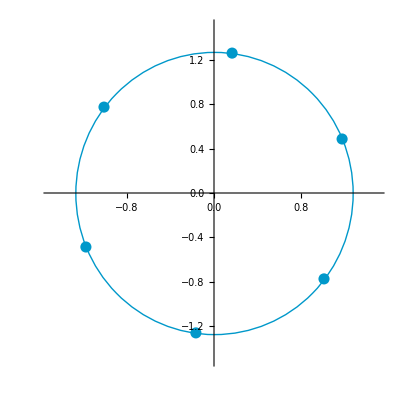

```mathematica
ListPlot[
t,
PlotRange->{
{-1.5, 1.5}, {-1.5, 1.5}
},
AspectRatio->1,
PlotStyle->{
PointSize[0.02],
RGBColor[0,0.596078, 0.792157]
},
Epilog->{
RGBColor[0,0.596078, 0.792157],
Circle[
{0,0},
Abs[Z[[1]]]
]
}
]
```

Logic:
1) 
        B) Vilka av dessa propositioner är sanna?

```mathematica
p1: (√2∈ℝ)∧∼(√2∈Q)
```

```mathematica
FullSimplify[Element[√2,Reals]&& !Element[√2,Rationals]]
```

True

```mathematica
p2: 1/2 ∈ Z ∨ 1/2∈Q 
FullSimplify[Element[1/2,Integers]∨ Element[1/2,Rationals]]
```

p2:1/2∈{-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}||1/2∈Q

True

```mathematica
p3:~(-4∈N)⟶~(-4∈Z)
```

```mathematica
Implies[!NonNegative[-4],!Element[-4,Integers]]
```

False

```mathematica
p4: 2.5∈Q↔ 2.5∈R
```

Element::argrx: Element called with 3 arguments; 2 arguments are expected.

```mathematica
Equivalent[Element[5/2,Rationals],Element[2.5,Reals]]
```

True

Ekvationlösning och grafer: 

En D’Artagnan jagas av Richeliue. Båda rider så snabbt de kan. D’Artagnan rider med en hastighet av 42 km/h och Richeliue med 57 km/h. Richeliue är 60 meter efter D’Artagnan och det är 250 meter till stadsporten där D’Artagnan kan komma undan. Bestäm om Richeliue hinner i kapp D’Artagnan och i så fall vilken tidpunkt och sträcka innan stadsporten det sker. Illustrera tidsförloppet grafiskt på lämpligt sätt.

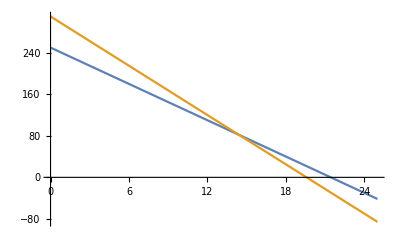

```mathematica
fDa[x_]:=250-(42/3.6)x
fRi[x_]:=310-(57/3.6)x
Plot[{fDa[x],fRi[x]}, {x,0,25}]
```

```mathematica
Solve[fDa[x]==fRi[x]]
```

{{x→14.4}}

```mathematica
fDa[14.4]
```

82.

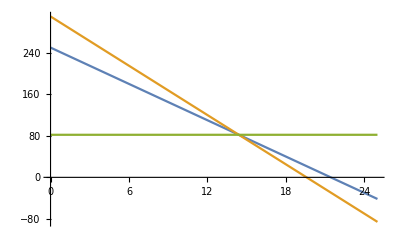

```mathematica
Plot[{fDa[x],fRi[x],82},{x,0,25}]
```

Svar : 82 meters / 14.4 sekunders marginal hinner han med